## Effective Potential with metrics

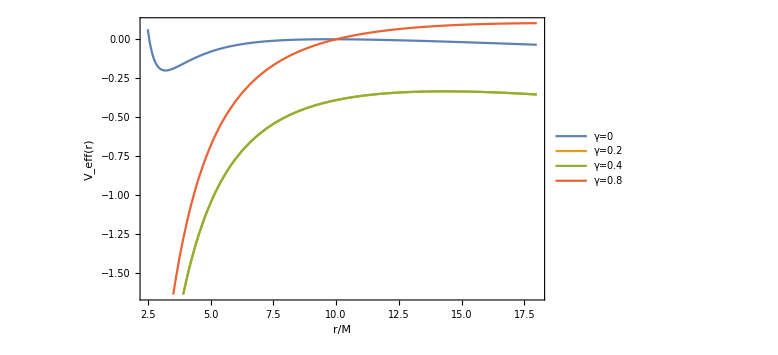

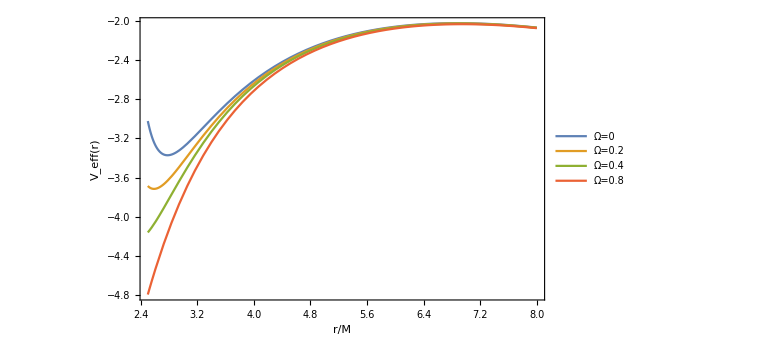

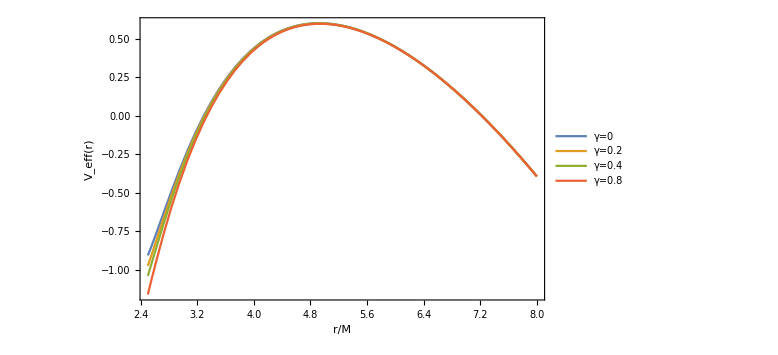

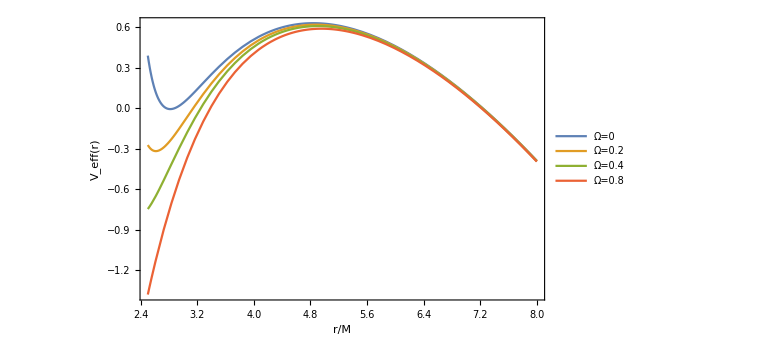

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
Veff[r_,L_,Ene_,ω_,Ω_,γ_] = -1 + Ene^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2; (*ω = eB/(2mc)*)

veff[r_,L_,ω_,Ω_,γ_] = f[r,Ω,γ] (1 + ((L+ ω r^2)^2)/r^2);
Plot[veff[r,6,0.0,0.,0.0],{r,2.5,8}];
Plot[{Veff[r,4,1,0.01,0.6,0],Veff[r,6,1,0.02,0.6,0.2],Veff[r,6,1,0.02,0.6,0.4],Veff[r,6,1,-0.01,0.6,0.8]},{r,2.5,18},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, Ω=0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"γ=0","γ=0.2","γ=0.4","γ=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]]

Plot[{Veff[r,6,1,0.1,0.0,0.6],Veff[r,6,1,0.1,0.2,0.6],Veff[r,6,1,0.1,0.4,0.6],Veff[r,6,1,0.1,0.8,0.6]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = 0.1, γ = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"Ω=0","Ω=0.2","Ω=0.4","Ω=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]]

Plot[{Veff[r,6,1,-0.2,0.6,0],Veff[r,6,1,-0.2,0.6,0.2],Veff[r,6,1,-0.2,0.6,0.4],Veff[r,6,1,-0.2,0.6,0.8]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = -0.2, Ω = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"γ=0","γ=0.2","γ=0.4","γ=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]]


Plot[{Veff[r,6,1,-0.2,0.0,0.6],Veff[r,6,1,-0.2,0.2,0.6],Veff[r,6,1,-0.2,0.4,0.6],Veff[r,6,1,-0.2,0.8,0.6]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = -0.2, γ = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"Ω=0","Ω=0.2","Ω=0.4","Ω=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]]
```

```mathematica
.
```

## Angular momentum and energy

### Energy of charged particle

{r→6.}

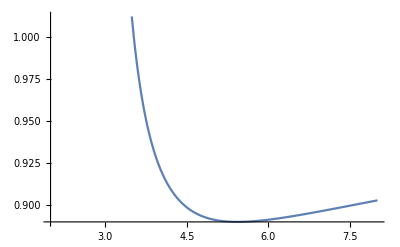

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
Ene[r_,Ω_,γ_,ω_] = (f[r,Ω,γ] (1+((k[r,Ω,γ,ω] + ω r^2)^2)/r^2))^0.5;

 FindRoot[D[Ene[r,0.,0,0.0],r]==0,{r,6}]
Plot[Ene[r,0.1,0,0.02],{r,2,8}]
```

### Angular Momentum

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;

Plot[L[-0.1,0.4,0.2,r]^2,{r,1.5,4}];
```

```mathematica
Solve[D[Veff[r,L,Ene,ω,Ω,γ],r]==0,Ene];
```

```mathematica
ee = -((ⅈ √2 √(L^2-r^4 ω^2))/(r^(3/2) √((4 Ω)/(r^4 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)+(6 γ Ω)/(r^5 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)-2/(r^2 (1+Ω/r^2+(γ Ω)/r^3) (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2))));
Solve[-1 + ee^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2==0,L];//Simplify
```

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
FindRoot[D[k[r,0,0,0],r]==0,{r,6}]
gg = Table[γ,{γ,0,0.65,0.001}];
rr = Table[r/.FindRoot[(D[k[r,0.1,γ,0.1],r]/.{γ->gg[[i]]})==0,{r,6}],{i,1,Length[gg]}];
rrgg = Table[{gg[[i]],rr[[i]]},{i,1,Length[gg]}];
ListLinePlot[rrgg,Frame->True,FrameLabel->{"γ","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],ImageSize->Large];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→6.}

## ISCO radii

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
rr[Ω_,γ_,ω_]=r/.FindRoot[D[k[r,Ω,γ,ω],r]==0,{r,6.}];
z1 =1+(1-Ω^2)^(1/3)((1+Ω)^(1/3)+(1-Ω)^(1/3));
z2 = Sqrt[3 Ω^2 + z1^2];
rk[Ω_]= 3+z2-Sqrt[(3-z1)(3+z1+2 z2)];       (*Kerr - ISCO*)
Plot[rk[Ω],{a,0,0.5}];
Plot[{rr[Ω,0,0],rr[Ω,0.2,-0.02],rr[Ω,0.4,-0.01],rr[Ω,0.6,0.01],rr[Ω,0.75,0.02],rk[Ω]},{Ω,0.,0.92},Frame->True,FrameLabel->{"Ω, a/M","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0, ω=0","γ=0.2, ω=-0.02","γ=0.4, ω=-0.01","γ=0.6, ω=0.01","γ=0.8, ω=0.02","Kerr BH"},{Scaled[{0.05,0.15}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange},{Dashed,Black}},ImageSize->Large];

Plot[{rr[0,γ,0.0],rr[0.2,γ,-0.01],rr[0.4,γ,-0.02],rr[0.6,γ,0.01],rr[0.8,γ,0.02],rk[γ]},{γ,0.,0.6},Frame->True,FrameLabel->{"γ, a/M","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0, ω=0","γ=0.2, ω = -0.01","γ=0.4, ω= -0.02","γ=0.6, ω=0.01","γ=0.8, ω=0.02","Kerr BH"},{Scaled[{0.05,0.15}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange},{Dashed,Black}},ImageSize->Large];
```

FindRoot::nlnum: The function value {-(23328. (216.-6. Ω-2. γ Ω) ((0.000771605 (1.69305×10^9 Power[«2»]+«10»+108. Power[«2»] Plus[«4»]))/(216.+Times[«2»]+Times[«3»])^2-(0.00154321 «1» («1»))/(«1»)^3-(0.000514403 («1»))/(«1»)^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+«11»+216. Power[«2»] Plus[«4»])/(216.+Times[«2»]+Times[«3»])^2))+«5»} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-6. Ω-2. γ Ω) ((0.000771605 (1.69305×10^9 Power[«2»]+«10»+108. Power[«2»] Plus[«4»]))/(216.+Times[«2»]+Times[«3»])^2-(0.00154321 «1» («1»))/(«1»)^3-(0.000514403 («1»))/(«1»)^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+«11»+216. Power[«2»] Plus[«4»])/(216.+Times[«2»]+Times[«3»])^2))+«5»} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

### Degeneracy plots between Kerr Bh and RGI bh.

FindRoot::nlnum: The function value {(1296. (216.-6. Charting`Private`pvar$5768) (27216.+1620. Charting`Private`pvar$5768+12. (Charting`Private`pvar$5768)^2) (-0.01+0.0277778 √(Power[«2»] Plus[«9»])))/((23328.+2376. Charting`Private`pvar$5768+36. (Charting`Private`pvar$5768)^2)^2)-(«1»)/(«1»)-(«1»)/(«1»)-(23328. («5»-«1») (-(0.000514403 («1»))/(«1»)^2-(«1»)/(«1»)^3+(0.000771605«1»«1»)/(«5»+«1»)^2))/((23328.+2376. Charting`Private`pvar$5768+36. (Charting`Private`pvar$5768)^2) √((«1»)/(«1»)^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Charting`Private`pvar$5768,0,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1296. (216.-6. Charting`Private`pvar$5768) (27216.+1620. Charting`Private`pvar$5768+12. (Charting`Private`pvar$5768)^2) (-0.01+0.0277778 √(Power[«2»] Plus[«9»])))/((23328.+2376. Charting`Private`pvar$5768+36. (Charting`Private`pvar$5768)^2)^2)-(«1»)/(«1»)-(«1»)/(«1»)-(23328. («5»-«1») (-(0.000514403 («1»))/(«1»)^2-(«1»)/(«1»)^3+(0.000771605«1»«1»)/(«5»+«1»)^2))/((23328.+2376. Charting`Private`pvar$5768+36. (Charting`Private`pvar$5768)^2) √((«1»)/(«1»)^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Charting`Private`pvar$5768,0,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-6.8 «26») ((0.000771605 (169305.+«10»+108. Power[«2»] Plus[«3»]))/(216.+Times[«2»])^2-(«20» («1»))/(«1»)^2-(0.00154321 (108.-«1») (72559.4+«11»+«1»))/(216.+Times[«2»])^3))/((23328.+2548.8 Charting`Private`pvar$5768+40.96 (Charting`Private`pvar$5768)^2) √((72559.4+«11»+216. Power[«2»] Plus[«3»])/(216.+Times[«2»])^2))+(«1»)/(«1»)^2-(«1»)/(«1»)-(1296. («1») (-0.01+0.0277778 √(«1»)))/(23328.+2548.8 «26»+40.96 («26»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,Charting`Private`pvar$5768,0.4,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

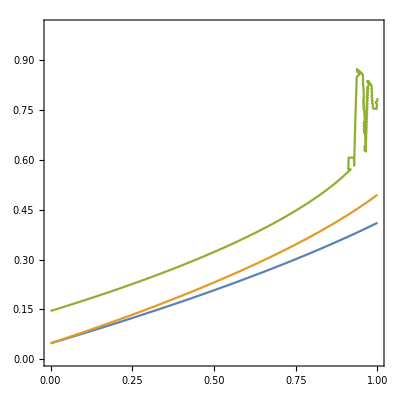

FindRoot::nlnum: The function value {(36. (214.2-0.6 Charting`Private`pvar$5845) (27735.5+0.18 «26»+32.4 (-1.+2. Charting`Private`pvar$5845)) √((5.15082×10^6+«7»+2332.8 Plus[«2»]+19.44 Plus[«3»])/(214.2+Times[«2»])^2))/((24108.8+1.08 Charting`Private`pvar$5845+0.09 («26»)^2+64.8 (-1.+Times[«2»]))^2)-«1»-«1»-(23328. («1») ((0.000771605 («1»))/(«6»+«1»)^2-(«1»)/(«1»)-(«20» («1»))/(((«1»«1»)^2)))/((24108.8+1.08 Charting`Private`pvar$5845+«5» «1»+64.8 (-1.+Times[«2»])) «1»)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.3,Charting`Private`pvar$5845,0]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(36. (214.2-0.6 Charting`Private`pvar$5845) (27735.5+0.18 «26»+32.4 (-1.+2. Charting`Private`pvar$5845)) √((5.15082×10^6+«7»+2332.8 Plus[«2»]+19.44 Plus[«3»])/(214.2+Times[«2»])^2))/((24108.8+1.08 Charting`Private`pvar$5845+0.09 («26»)^2+64.8 (-1.+Times[«2»]))^2)-«1»-«1»-(23328. («1») ((0.000771605 («1»))/(«6»+«1»)^2-(«1»)/(«1»)-(«20» («1»))/(((«1»«1»)^2)))/((24108.8+1.08 Charting`Private`pvar$5845+«5» «1»+64.8 (-1.+Times[«2»])) «1»)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.3,Charting`Private`pvar$5845,0]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (212.4-1.2 «26») ((0.000771605 (935210.+2.23949×10^6 Plus[«2»]+«8»+55987.2 Plus[«2»]))/(212.4+Times[«2»])^2-(«20» («1»))/(«1»)^3-(0.000514403 (445031.+«10»+«8» «1»))/(212.4+Times[«2»])^2))/((24896.2+4.32 Charting`Private`pvar$5845+0.36 (Charting`Private`pvar$5845)^2+129.6 (-1.+Times[«2»])) √((445031.+«10»+55987.2 Plus[«2»])/(212.4+Times[«2»])^2))+«5»} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.6,Charting`Private`pvar$5845,0.02]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

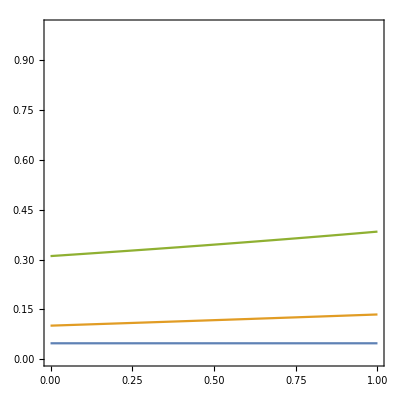

FindRoot::nlnum: The function value {-0.355347 (-1. Charting`Private`pvar$5921+0.000130657 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))-(42839.6 (1.70714×10^-8 (2.29771×10^9 Power[«2»]+«9»+27. Plus[«4»])-2.8645×10^-8 («1»)))/(√(1.08839×10^9 (Charting`Private`pvar$5921)^2+«10»+54. (-0.5+Times[«2»]+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.5,0.4,Charting`Private`pvar$5921]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.355347 (-1. Charting`Private`pvar$5921+0.000130657 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))-(42839.6 (1.70714×10^-8 (2.29771×10^9 Power[«2»]+«9»+27. Plus[«4»])-2.8645×10^-8 («1»)))/(√(1.08839×10^9 (Charting`Private`pvar$5921)^2+«10»+54. (-0.5+Times[«2»]+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.5,0.4,Charting`Private`pvar$5921]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.536489 (-1. Charting`Private`pvar$5921+0.000131923 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))-(40729.7 (1.74038×10^-8 (2.41865×10^9 Power[«2»]+«9»+69.12 Plus[«4»])-«23» («1»)))/(√(1.16095×10^9 (Charting`Private`pvar$5921)^2+«10»+138.24 (-0.8+Times[«2»]+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.8,0.4,Charting`Private`pvar$5921]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

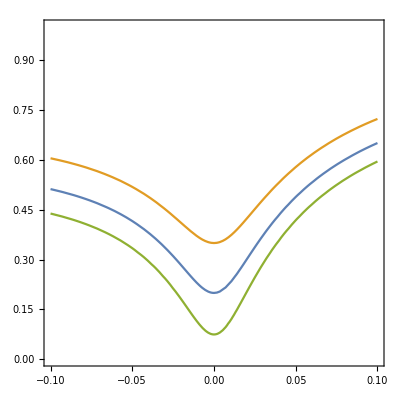

```mathematica
ContourPlot[{rk[a]-rr[Ω,0,0.01]==0,rk[a]-rr[Ω,0.4,0.01]==0,rk[a]-rr[Ω,0.8,0.02]==0},{Ω,0,1},{a,0,1}]

ContourPlot[{rk[a]==rr[0,γ,0.01],rk[a]==rr[0.3,γ,0],rk[a]==rr[0.6,γ,0.02]},{γ,0,1},{a,0,1}]

ContourPlot[{rk[a]==rr[0.5,0.4,ω],rk[a]==rr[0.8,0.4,ω],rk[a]==rr[0.2,0.4,ω]},{ω,-0.1,0.1},{a,0,1}]
```